14.1942

2.27108

7.09712

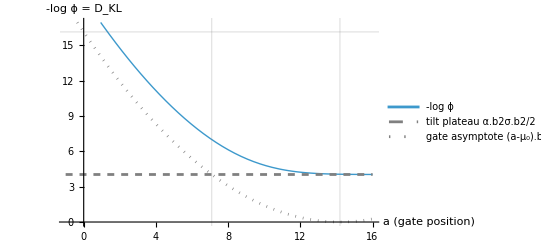

```mathematica
(*---parameters---*)
σ=2.5;
L0=10^7.;
ζ=0.5;
μ0=σ Sqrt[2 Log[L0]]     (*naïve peak;EVT edge sits at a=0*)
β=Sqrt[2 Log[L0]]/σ     (*entropy slope β**)
α=ζ β;                    (*one round of EP*)
μ1=μ0-α σ^2             (*tilted mean*)

(*---building blocks---*)
nd=NormalDistribution[0,1];
ρ[x_]:=PDF[nd,x]/CDF[nd,x];          (*inverse Mills ratio*)
w[a_]:=(a-μ1)/σ;
mlogϕ[a_]:=α^2 σ^2/2+α σ ρ[w[a]]-Log[CDF[nd,w[a]]];

(*---two limiting references---*)
tiltPlateau=α^2 σ^2/2;                  (*slack-gate limit*)
gateAsymp[a_]:=(a-μ0)^2/(2 σ^2);      (*deep-cut limit,valid for a<μ0*)

(*---plot---*)
Plot[{mlogϕ[a],tiltPlateau,gateAsymp[a]},{a,-1,16},PlotStyle->{Thick,{Dashed,Gray},{Dotted,Gray}},PlotRange->{0,1.05 Log[L0]},AxesLabel->{"a  (gate position)","-log ϕ = D_KL"},GridLines->{{0,μ1,μ0},{Log[L0]}},PlotLegends->{"-log ϕ","tilt plateau α.b2σ.b2/2","gate asymptote (a-μ₀).b2/2σ.b2"}]
```

1.15

1.51158×10^7

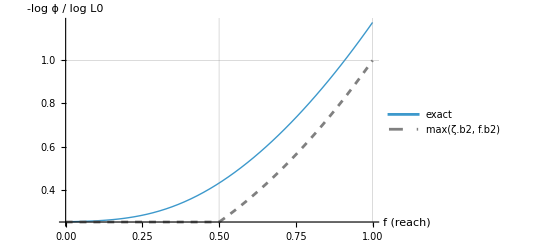

```mathematica
(*from data*)ζ=0.5;β=2.3;σ=2.5;          (*β*,σ measured/assumed*)
α=ζ β
L0=Exp[β^2 σ^2/2]                 (*ln L0=.bd β*.b2 σ.b2*)
μ0=β σ^2;
μ1=μ0-α σ^2;

nd=NormalDistribution[0,1];
ρ[x_]:=PDF[nd,x]/CDF[nd,x];
(*cost as a function of fractional reach f,in units of ln L0*)
s=β σ;                              (* =Sqrt[2 Log L0]*)
mlogϕN[f_]:=(α^2 σ^2/2+α σ ρ[(ζ-f) s]-Log[CDF[nd,(ζ-f) s]])/(β^2 σ^2/2);

Plot[{mlogϕN[f],Max[ζ^2,f^2]},{f,0,1},PlotStyle->{Thick,{Dashed,Gray}},GridLines->{{ζ,1},{ζ^2,1}},AxesLabel->{"f  (reach)","-log ϕ / log L0"},PlotLegends->{"exact","max(ζ.b2, f.b2)"}]
```

√10

26.

33.8

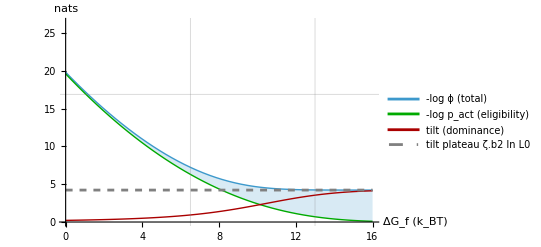

```mathematica
(*---parameters from data/heuristic pin---*)
ζ=0.5;α = 1.3;σ1=Sqrt[5];  σ2=Sqrt[10]      (*σ from ln L0=.bd β*.b2 σ.b2≈16.5*)
β=α/ζ ;
μ01=β σ1^2  ; μ02=β σ2^2                          (*naïve peak;EVT edge at a=0*)
μ11=μ01-α σ1^2;  μ12=μ02-α σ2^2;                      (*tilted mean (w=0 crossover)*)
lnL01=β^2 σ1^2/2; lnL02=β^2 σ2^2/2

(*---building blocks---*)
nd=NormalDistribution[0,1];
ρ[x_]:=PDF[nd,x]/CDF[nd,x];
w1[a_]:=(a-μ11)/σ1; w2[a_]:=(a-μ12)/σ2;
zp1[a_]:=(a-μ01)/σ1; zp2[a_]:=(a-μ02)/σ2;

(*full cost (dominance) and gate-only cost (eligibility)*)
mlogϕ1[a_]:=α^2 σ1^2/2+α σ1 ρ[w1[a]]-Log[CDF[nd,w1[a]]]; mlogϕ2[a_]:=α^2 σ2^2/2+α σ2 ρ[w2[a]]-Log[CDF[nd,w2[a]]];
gateKL1[a_]:=-Log[CDF[nd,zp1[a]]];   gateKL2[a_]:=-Log[CDF[nd,zp2[a]]];  (* =-log p_act,exact*)
tiltKL1[a_]:=α^2 σ1^2/2+α σ1 ρ[w1[a]]-Log[CDF[nd,w1[a]]/CDF[nd,zp1[a]]]; tiltKL2[a_]:=α^2 σ2^2/2+α σ2 ρ[w2[a]]-Log[CDF[nd,w2[a]]/CDF[nd,zp2[a]]];

Plot[{mlogϕ1[y],gateKL1[y], tiltKL1[y],α^2 σ1^2/2},{y,0,16},PlotStyle->{Thick,{Thick,Darker@Green},{Thick,Darker@Red},{Dashed,Gray}},Filling->{1->{2}},(*shaded gap=tilt term*)PlotRange->{0,1.25 lnL0},AxesLabel->{"ΔG_f  (k_BT)","nats"},GridLines->{{0,μ11,μ01},{lnL01}},PlotLegends->{"-log ϕ (total) ","-log p_act (eligibility)","tilt (dominance)", "tilt plateau ζ.b2 ln L0"}]
```

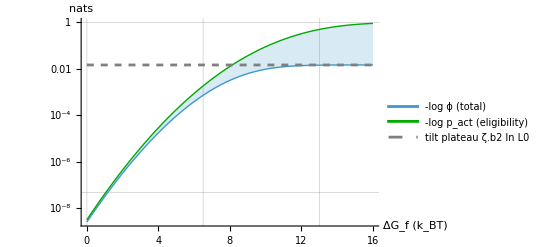

```mathematica
LogPlot[{Exp[-mlogϕ1[y]],Exp[-gateKL1[y]],Exp[-α^2 σ1^2/2]},{y,0,16},PlotStyle->{Thick,{Thick,Darker@Green},{Dashed,Gray}},Filling->{1->{2}},(*shaded gap=tilt term*)PlotRange->Automatic,AxesLabel->{"ΔG_f  (k_BT)","nats"},GridLines->{{0,μ11,μ01},{1/Exp[lnL01],1}},PlotLegends->{"-log ϕ (total) ","-log p_act (eligibility)", "tilt plateau ζ.b2 ln L0"}]
```

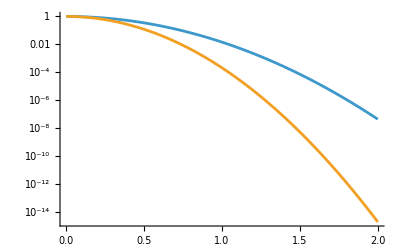

```mathematica
ϕ1[n_]:=Exp[-(1/2) n^2 σ1^2 (β ζ)^2]; ϕ2[n_]:=Exp[-(1/2) n^2 σ2^2 (β ζ)^2];
LogPlot[{ϕ1[n], ϕ2[n]}, {n, 0, 2}]
```

```mathematica
cols={Red,Blue,Darker@Green,Orange,Purple};
Show[
LogPlot[{ϕ1[n], ϕ2[n]},{n,0,2},PlotRange->All, PlotLegends->Placed[LineLegend[Automatic,Table[Row[{b}],{b, {5, 10}}],LegendLabel->"l"],{Right,Top}],Frame->{{True,False},{True,False}},FrameTicks->{{1, 2}, Automatic}, PlotStyle->{Gray, Black}
],ListLogPlot[{Callout[{0,ϕ1[0]},"Naive",{0.08, 0.01}],Callout[{1,ϕ1[1]},"primary",Above],Callout[{2,ϕ1[2]},"",Left],Callout[{1,ϕ2[1]},"",Above],Callout[{2,ϕ2[2]},"memory",Left]}, PlotStyle->(Directive[#,PointSize[0.016]]&/@cols)
]
]
```

-Graphics-

```mathematica
016
```

```mathematica
Ω0[x_]:=1/Sqrt[2*Pi *σ1^2] Exp[-(x-μ01)^2/(2*σ1^2)]
```

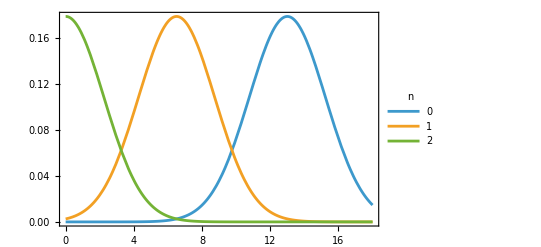

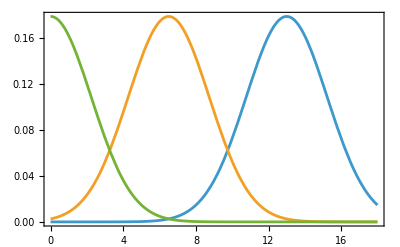

```mathematica
Plot[{Ω0[x], Ω0[x]*Exp[-α x]Exp[-1/2 σ1^2 α^2+ α μ01],  Ω0[x]*Exp[-α x]Exp[-1/2 σ1^2 α^2+ α μ01]Exp[-α x]Exp[-1/2 σ1^2 α^2+ α μ11]}, {x, -0.01, 18},
Frame->{{True,False},{True,False}}, Axes->False,PlotLegends->Placed[LineLegend[Automatic,Table[Row[{b}],{b,{0,1, 2}}],LegendLabel->"n"],{Right,Top}]]
```

```mathematica
cols=ColorData[97]/@{1,2,2,3,3};
Show[LogPlot[{ϕ1[n],ϕ2[n]},{n,0,2},PlotRange->All,PlotLegends->Placed[LineLegend[Automatic,Table[Row[{b}],{b,{5,10}}],LegendLabel->"l"],{Right,Top}],Frame->{{True,False},{True,False}},FrameTicks->{{1,2},Automatic},PlotStyle->{Gray,Black}],ListLogPlot[List/@{(* <--the only change*)Callout[{0,ϕ1[0]},"Naive",{0.08,0.01}],Callout[{1,ϕ1[1]},"primary",Above],Callout[{2,ϕ1[2]},"",Left],Callout[{1,ϕ2[1]},"",Above],Callout[{2,ϕ2[2]},"memory",Left]},PlotStyle->(Directive[#,PointSize[0.016]]&/@cols)]]
```

-Graphics-